# Ellipticality

https://twitter.com/nntaleb/status/1263097582613606400

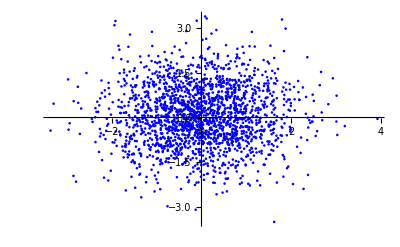
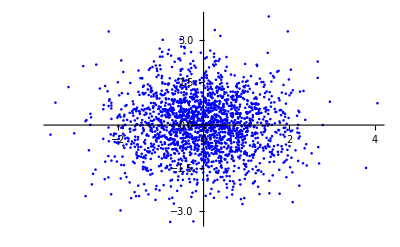
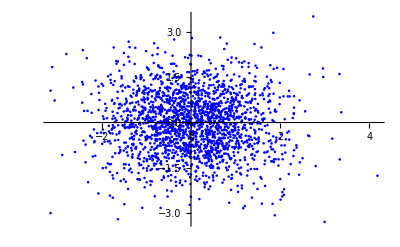
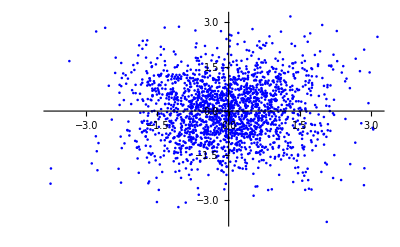
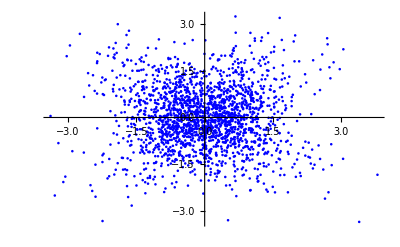
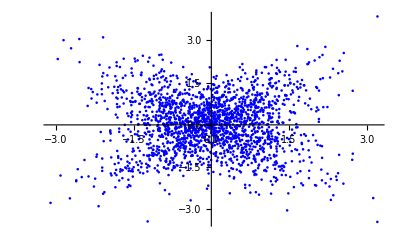
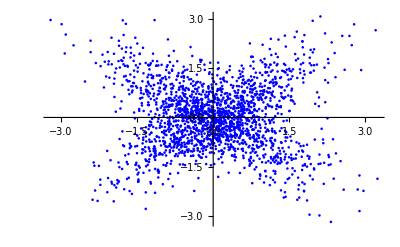
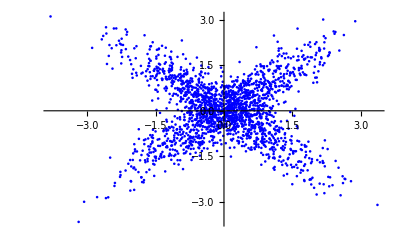

```mathematica
Table[ListPlot[Join[RandomVariate[BinormalDistribution[ρ], 1000], RandomVariate[BinormalDistribution[-ρ],1000]],PlotStyle->Blue],{ρ,0.19,1,0.1}]
```

General::munfl: Exp[-1224.65] is too small to represent as a normalized machine number; precision may be lost.

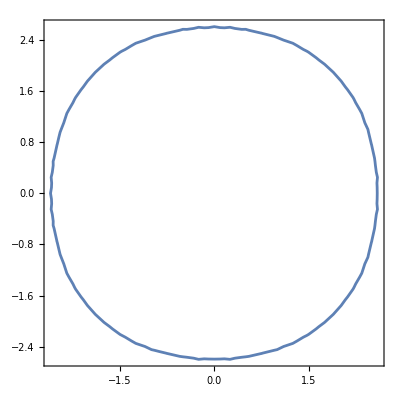
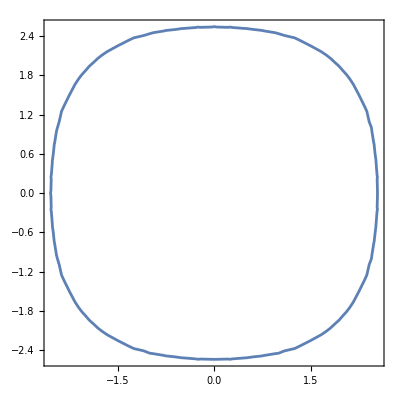
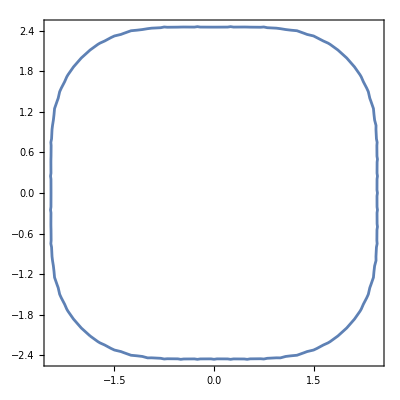
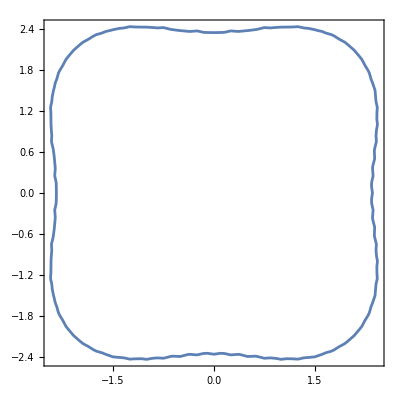
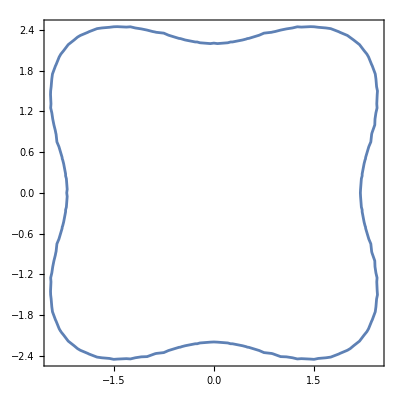
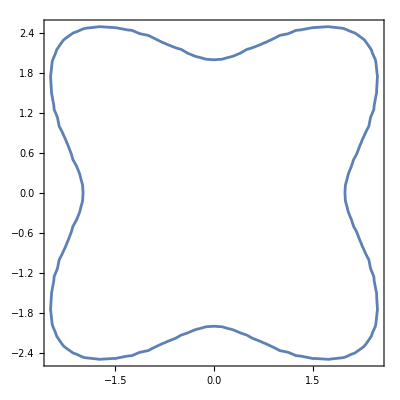
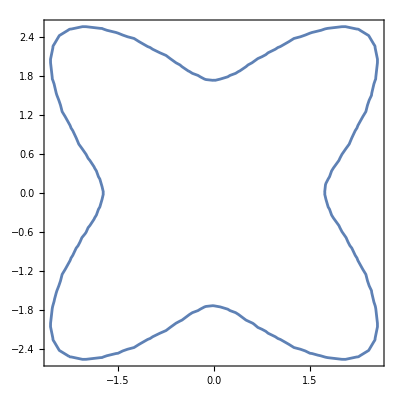
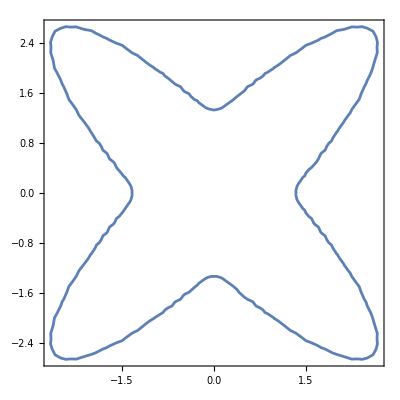

```mathematica
Table[ContourPlot[PDF[BinormalDistribution[ρ],{x,y}]+PDF[BinormalDistribution[-ρ],{x,y}]==0.01,{x, -3.5, 3.5}, {y, -3.5, 3.5}, PlotRange->All],{ρ, 0.19,1, 0.1}]
```